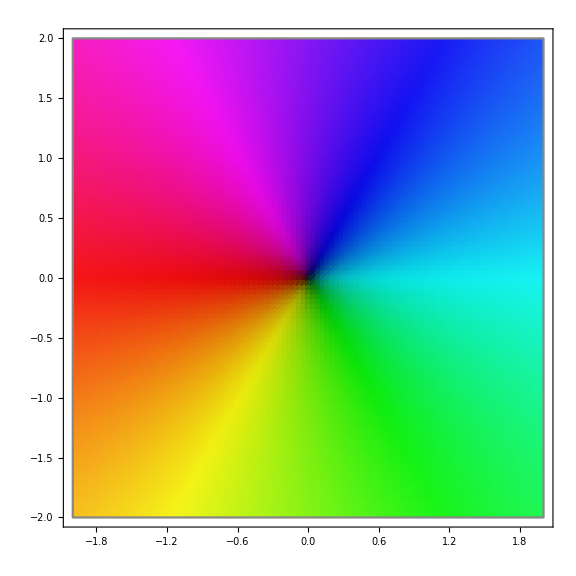

```mathematica
(* Adapted from http://math-www.uni-paderborn.de/~axel/graphs/ *)
DomainColoring[f_,xmin_,xmax_,ymin_,ymax_,points_:200]:=
RegionPlot[True,{x,xmin,xmax},{y,ymin,ymax},
ColorFunction->Function[{x, y}, w = f[x+ⅈ*y]; Hue[0.5+Arg[w]/(2π),1/(1+0.05Abs[w]),1-1/(1+10Abs[w])]], 
ColorFunctionScaling->False,
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},
(* FrameLabel->{"Re(z)","Im(z)",ToString@StandardForm@f@"z"}, *)
AspectRatio->Automatic,
PlotRange->{{xmin,xmax},{ymin,ymax}}, ImageSize->Large,
PlotPoints->points];
DomainColoring[(#)&, -2, 2, -2, 2, 100]
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#)&, -2, 2, -2, 2];
Export["Figure-2.jpg",image];
image = DomainColoring[(#)&, -100, 100, -100, 100]
Export["Figure-2-Extended.jpg",image]
```

-Graphics-

Figure-2-Extended.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#^2+1)&, -2, 2, -2, 2, 200];
Export["Figure-3.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(ⅈ*#)&, -2, 2, -2, 2, 200];
Export["Figure-4.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[Conjugate, -2, 2, -2, 2, 200];
Export["Figure-5.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#^2+1)&, -2, 2, -2, 2, 200];
Export["Figure-6.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#^5-#^4+ #^3-#^2+#)&, -2, 2, -2, 2, 200];
Export["Figure-7.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#^3+ⅈ#^2+ #+ⅈ)&, -2, 2, -2, 2, 200];
Export["Figure-8.jpg",image];
```

```mathematica
SetDirectory[NotebookDirectory[]];
image = DomainColoring[(#^2+1)/(#+1)&, -2, 2, -2, 2, 200]
Export["Figure-9.jpg",image];
```

-Graphics-

```mathematica
(* With this code we can create composed figures with the identity plane at the right side *)
CreateFigure[f_,xmin_,xmax_,ymin_,ymax_,points_:100]:= 
Grid[{{
DomainColoring[f,xmin,xmax,ymin,ymax,points], 
Graphics[{Arrowheads-> Large, Arrow[{{0,0},{1, 0}}]}, ImageSize->Medium,BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}, Epilog->{Text["f(z) = "<>ToString@StandardForm@f@"z", {0.5, 0.2}]}],
DomainColoring[Identity,xmin,xmax,ymin,ymax,points]
}}];
CreateFigure[(#^2+1)&, -2, 2, -2, 2, 200]
```

-Graphics-